```mathematica
EF[{x_,y_}] := {x,y}/((x^2+y^2)^(3/2))
```

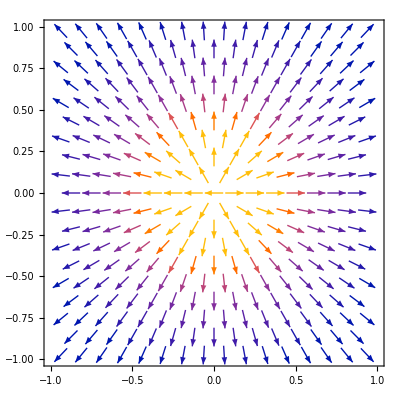

```mathematica
VectorPlot[EF[{x,y}],{x,-1,1},{y,-1,1}]
```

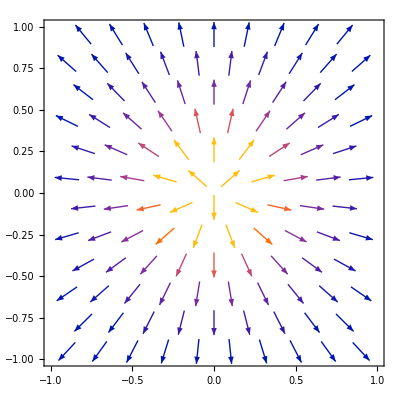

```mathematica
VectorPlot[EF[{x,y}],{x,-1,1},{y,-1,1}, VectorPoints->10]
```

```mathematica
EFSame[{x_,y_}] := {x,y}/((x^2+y^2)^(3/2))+{x-0.7,y}/(((x-0.7)^2+y^2)^(3/2))
```

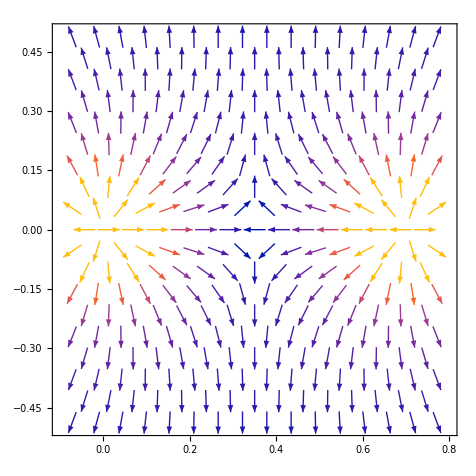

```mathematica
VectorPlot[EFSame[{x,y}],{x,-0.1,0.8},{y,-0.5,0.5}]
```

```mathematica
EFDiff[{x_,y_}] := {x,y}/((x^2+y^2)^(3/2))-{x-0.7,y}/(((x-0.7)^2+y^2)^(3/2))
```

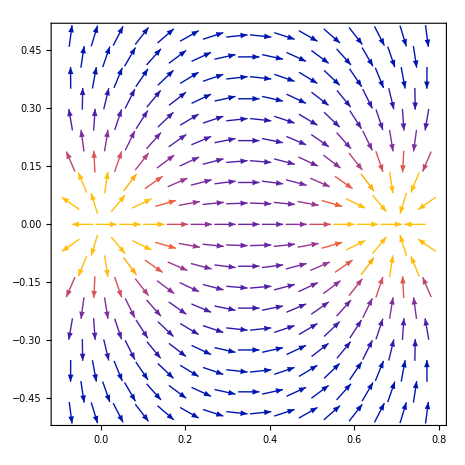

```mathematica
VectorPlot[EFDiff[{x,y}],{x,-0.1,0.8},{y,-0.5,0.5}]
```

```mathematica
EF[{x_,y_,z_}] := {x,y,z}/((x^2+y^2+z^2)^(3/2))
```

```mathematica
VectorPlot3D[EF[{x,y,z}], {x,-1,1}, {y,-1,1},{z,-1,1}, VectorScaling->Automatic]
```

-Graphics3D-